# 1D Hopper

## Baby Steps Towards Raibert's Hopper

## Simple Inelastic Hopper

Initial steps moving towards Raibert's hopper.  This first step just implements the ballistic 
and ground contact phases with a transition between them that is completely inelastic.  It 
doesn't look too real when simulated. Simulates two ballistic phases and one contact phase.

### Setup

```mathematica
(*--Load libraries--*)
AppendTo[$Path,ToFileName[{$HomeDirectory,"Mathematica"}]];
<<ivamatica/Mechanics/lagrangian.m
<<ivamatica/Graphics/anim.m
```

```mathematica
(*--Configuration space.--*)
q = {x, d};
q' = Table[ q[[i]]' , {i, Length[q]}];
ϕ = q[[1]] - q[[2]] ;
```

```mathematica
(*--Constants of the system.--*)
doSim = True;   (* If true, then do numerically, else do symbolically. *)
If[doSim,
  mb = 5; m = 1; g = 9.8;  (* Numerical values to use *)
,
 Clear[mb, m, g] (* Clear out the variables so remain symbolic. *)
];
```

```mathematica
(*--Lagrangian--*)
L = 1/2 mb (x')^2 + 1/2 m (x' - d')^2 - mb g x - m g (x - d);
```

```mathematica
(*--Equations of motion using Lagrange multiplier.--*)
Clear[λ]
eqns = Simplify[fConsLagrangeEqns[L,{Fb, Fd} ,ϕ,{x,d}, {x',d'}, λ]]/. {x'' -> x''[t] , d'' -> d''[t]}
seqns = Solve[ eqns, {x''[t], d''[t]}][[1]];
seqns= Simplify[Table[ seqns[[i]][[1]] == seqns[[i]][[2]]  , {i, Length[seqns]}]]
```

{58.8+λ+6 x''[t]==Fb+d''[t],d''[t]==9.8+Fd+λ+x''[t]}

{x''[t]==-9.8+0.2 Fb+0.2 Fd,d''[t]==-7.10543×10^-15+0.2 Fb+1.2 Fd+1. λ}

```mathematica
(*--Solve for Lagrange multiplier and Fd so that we can prescribe accelerations (pseudo-inverse type of stuff).--*)
λsys[0] = 0;
λ = λsys[0];
eqnsolv ={seqns[[2]], d''[t] == 0} ;
Flatten[Solve[ eqnsolv , {Fd, q[[2]]''[t]}]]
Fsys[0] = %[[1,2]];

Clear[λ];
ϕt = ϕ ;
For[ i=1, i<=Length[q], i++, ϕt = ϕt /. {q[[i]] -> q[[i]][t]}];
eqnsolv =Append[seqns, D[D[ϕt,t],t] == 0] 
λsol = Flatten[Solve[ eqnsolv , Join[{λ},Table[ q[[i]]''[t] , {i, Length[q]}]]]]
λsys[1] =  λ /. λsol;
λ = λsys[1];
eqnsolv ={seqns[[2]], d''[t] == 0} ;
Flatten[Solve[ eqnsolv , {Fd, q[[2]]''[t]}]]
Fsys[1] = %[[1,2]];
Clear[λ];
```

{Fd→5.92119×10^-15-0.166667 Fb,d''[t]→0.}

{x''[t]==-9.8+0.2 Fb+0.2 Fd,d''[t]==-7.10543×10^-15+0.2 Fb+1.2 Fd+1. λ,-d''[t]+x''[t]==0}

{λ→-1. (0.-1. (7.10543×10^-15-0.2 Fb-1.2 Fd))-1. (9.8-0.2 Fb-0.2 Fd),x''[t]→-9.8+0.2 Fb+0.2 Fd,d''[t]→-9.8+0.2 Fb+0.2 Fd}

{Fd→49.-1. Fb,d''[t]→0.}

### Simulation w/Sanity Checks and Plots

#### Beginning of Simulation: In flight, go until hit ground.

1.44431

{{1.},{2.22045×10^-16},{1.},{-9.15423},{-9.15423},{0.}}

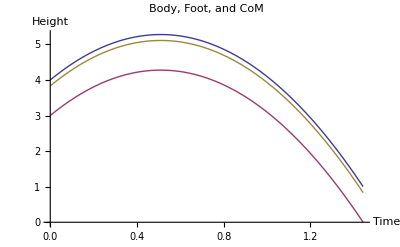

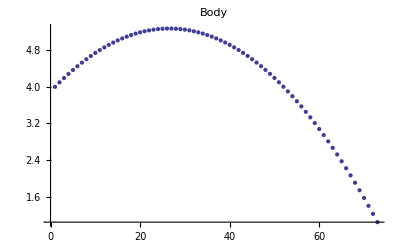

```mathematica
mb = 5; m = 1; g = 9.8;
ti =0; tf = 4;
state =0;

{x0, d0, x0p, d0p} = {4, 1, 5, 0};
Fb = 0;
Fc = 0;
Fd =  Fc + Fsys[state];
λ = λsys[state];
sols = NDSolve[Join[seqns, {x'[0] == x0p , d'[0] == d0p , x[0] == x0 , d[0] == d0}], {x,d}, {t,ti,tf}, Method->{"EventLocator","Event" -> (x[t] - d[t])}];

(* Grab final time from Interpolating function solution. *)
tf = sols[[1,1,2,1,1,2]] 

(* Perform sanity check by finding the zero crossing. Use solution as initial guess. *)
T =tf;
troot = FindRoot[ (x[t]/.sols)[[1]]-(d[t]/.sols)[[1]] == 0 ,{t, T, ti, tf}] ;
T = t /. troot;
{x[T] /. sols, (x[T] /. sols )-(d[T] /. sols) , d[T] /. sols, x'[T] /. sols, (x'[T] /. sols )-(d'[T] /. sols) , d'[T] /. sols}  (* Print values and derivatives. *)

(* Plot the system evolution. *)
Plot[{x[t]/. sols, (x[t]/.sols)-(d[t]/.sols) ,((  mb x[t] /. sols )  + (m (x[t]/.sols) - m (d[t] /. sols)))/(m+mb) }, {t,ti, T}, AxesLabel->{"Time", "Height"}, PlotRange -> All, PlotLabel-> "Body, Foot, and CoM"] 
Clear[ mb, m, Fb, Fd, Fn, g];
psol = Table[ {(x[t] /. sols)[[1]] , (d[t] /.sols)[[1]]} , {t, ti,T, 0.02}];
ListPlot[Table[ psol[[i]][[1]] , {i, Length[psol]}], PlotLabel->"Body"]
```

#### Second Phase of Simulation: On ground, go until no ground reaction.

```mathematica
(* Grab final conditions from last phase as initial for current. *)
{x0  , x0p, d0, d0p }= {(x[tf] /. sols )[[1]],0, (x[tf] /. sols)[[1]], 0}
d0p = 0;
```

{1.,0,1.,0}

{{x→InterpolatingFunction[{{1.44431,1.82133}},<>],d→InterpolatingFunction[{{1.44431,1.82133}},<>]}}

1.82133

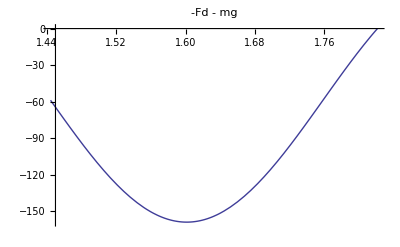

{t→1.82133}

1.82133

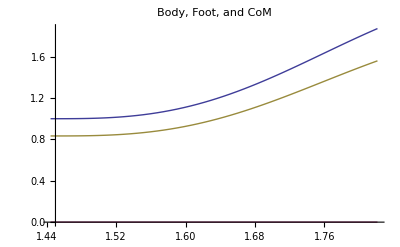

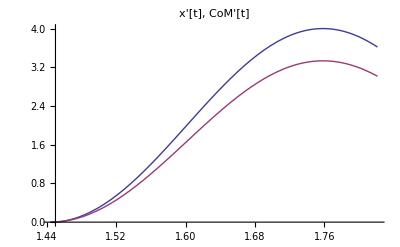

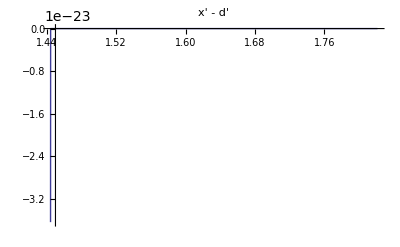

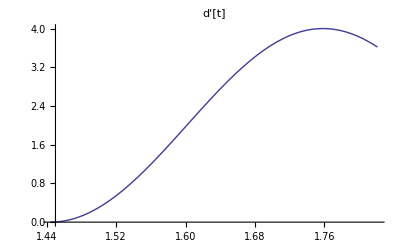

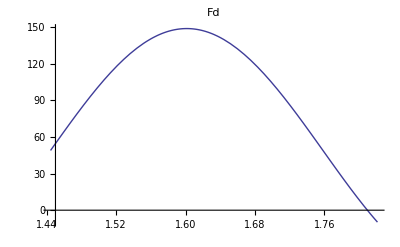

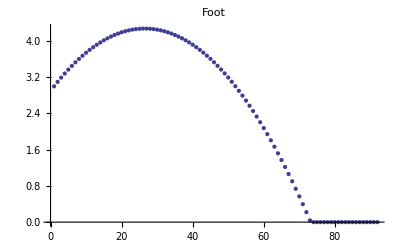

{x''[t]==-9.8+0.2 Fb+0.2 Fd,d''[t]==-7.10543×10^-15+0.2 Fb+1.2 Fd+1. (-1. (9.8-0.2 (49.+100 Sin[10 (-1.44431+t)]))-1. (0.-1. (7.10543×10^-15-1.2 (49.+100 Sin[10 (-1.44431+t)]))))}

```mathematica
mb = 5; m = 1; g = 9.8;
state = 1;
ti = N[tf];
tf =ti + N[2 π/10];
Fb = 0;
Fd = 100*Sin[10 (t-ti)]+ Fsys[state];
λ = λsys[state];
seqns;
-Fd - m g ≥ 0 /. {t -> ti};
sols = NDSolve[Join[seqns, {x'[ti] == x0p , d'[ti] == d0p , x[ti] == x0 , d[ti] == d0}], {x,d}, {t,ti,tf}, Method->{"EventLocator","Event" -> (-Fd -m g ≥ 0)}]

(* Grab final time from Interpolating function solution. *)
tf = sols[[1,1,2,1,1,2]]

(* Perform sanity check by finding the zero crossing. Use solution as initial guess. *)
T =tf;
Plot[-Fd - m g, {t, ti, tf}, PlotLabel->"-Fd - mg"]
troot = FindRoot[ -Fd - m g == 0 ,{t, T, ti, tf}] 
tf = t /. troot

(* Plot the system evolution. *)
Plot[{x[t]/. sols, (x[t]/.sols)-(d[t]/.sols) ,((  mb x[t] /. sols )  + (m (x[t]/.sols) - m (d[t] /. sols)))/(m+mb) }, {t, ti,tf}, PlotRange -> All, PlotLabel-> "Body, Foot, and CoM"] 
Plot[{x'[t]/. sols,((  mb x'[t] /. sols )  + (m (x'[t]/.sols) - m (d'[t] /. sols)))/(m+mb) }, {t, ti,tf}, PlotLabel->"x'[t], CoM'[t]"] 
Plot[  (x'[t]/.sols)-(d'[t]/.sols) ,{t,ti,tf},PlotLabel-> "x' - d'"]
Plot[  d'[t]/.sols ,{t,ti,tf}, PlotLabel-> "d'[t]"]
Plot[ Fd , {t, ti,tf}, PlotLabel->"Fd"]
Clear[ mb, m, Fb, Fd]
psol =Join[ psol,  Table[ {(x[t] /. sols)[[1]] , (d[t] /.sols)[[1]]} , {t, ti,tf, 0.02}] ];
ListPlot[Table[ psol[[i]][[1]] -psol[[i]][[2]], {i, Length[psol]}], PlotLabel->"Foot"]
seqns
```

#### Third phase: second time ballistic, go until hit ground.

```mathematica
(* Grab final conditions from last phase as initial for current. *)
{x0  , x0p, d0, d0p }= {(x[tf] /. sols )[[1]],(x'[tf] /. sols)[[1]],(x[tf] /. sols)[[1]],(d'[tf] /. sols)[[1]]}
d0p = 0;
```

{1.87164,3.61772,1.87164,3.61772}

{{x→InterpolatingFunction[{{1.82133,2.58632}},<>],d→InterpolatingFunction[{{1.82133,2.58632}},<>]}}

2.58632

2.55964

{{1.87164},{0.},{1.87164},{-3.61772},{-3.61772},{0.}}

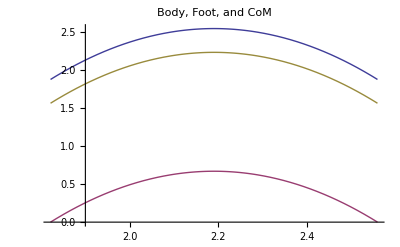

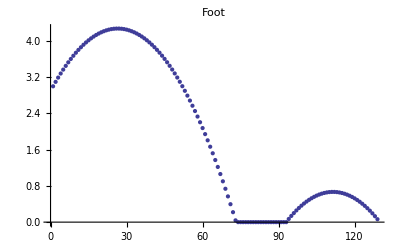

```mathematica
mb = 5; m = 1; g = 10;
ti =tf; tf = ti + 124;
state = 0;

Fb = 0;
Fd = Fsys[state];
λ = λsys[state];
sols = NDSolve[Join[seqns, {x'[ti] == x0p , d'[ti] == d0p , x[ti] == x0 , d[ti] == d0}], {x,d}, {t,ti,tf}, Method->{"EventLocator","Event" -> (x[t] - d[t]+0.1)}]
tf = sols[[1,1,2,1,1,2]]
T =tf;
troot = FindRoot[ (x[t]/.sols)[[1]]-(d[t]/.sols)[[1]] == 0 ,{t, T, ti, tf}] ;
T = t /. troot;
tf = T
{x[T] /. sols, (x[T] /. sols )-(d[T] /. sols) , d[T] /. sols, x'[T] /. sols, (x'[T] /. sols )-(d'[T] /. sols) , d'[T] /. sols} 

Plot[{x[t]/. sols, (x[t]/.sols)-(d[t]/.sols) ,((  mb x[t] /. sols )  + (m (x[t]/.sols) - m (d[t] /. sols)))/(m+mb) }, {t,ti,tf},PlotLabel-> "Body, Foot, and CoM"] 
Plot[ Fd, {t, ti, tf}];
Clear[ mb, m, Fb, Fd, Fn];
psol =Join[ psol,  Table[ {(x[t] /. sols)[[1]] , (d[t] /.sols)[[1]]} , {t, ti,T, 0.02}] ];
ListPlot[Table[ psol[[i]][[1]] -psol[[i]][[2]], {i, Length[psol]}], PlotLabel->"Foot"]
```

#### Final Result.

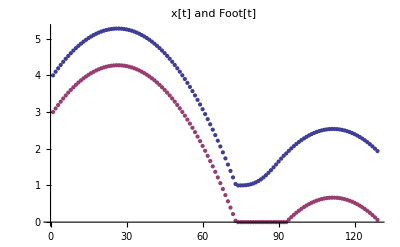

```mathematica
(* Plot the entire sequence. *)
ListPlot[ {Table[ psol[[i]][[1]], {i, Length[psol]}],Table[ psol[[i]][[1]] -psol[[i]][[2]], {i, Length[psol]}]}, Joined->{False,False}, PlotLabel->"x[t] and Foot[t]"]
```

### (*--Animation--*)

```mathematica
(*<<Graphics`Animation`*)
footlen = .25;
bodyrad = .25;
XMIN = -4; XMAX = 4; YMIN = -1; YMAX = 10;
```

```mathematica
gPogo[q_] := Graphics[ { Dashing[{0.05,0.15}] , Line[{{XMIN,0},{XMAX,0}}], Dashing[{0,0}],
  Line[{{-footlen , q[[1]] - q[[2]]},{footlen, q[[1]]-q[[2]]}}] , Line[{{0,q[[1]]-q[[2]]},{0,q[[1]]}}], Disk[{0,q[[1]]},bodyrad]}, PlotRange->{{XMIN,XMAX},{YMIN,YMAX}}, AspectRatio -> Automatic];
```

```mathematica
ListAnimate[ Table[ gPogo[psol[[i]]] , {i, 1, Length[psol]}]]
```

## Simple Elastic Hopper

Initial steps moving towards Raibert's hopper.  This version implements the ballistic 
and ground contact phases with a transition between them that is elastic, as though 
the leg had some internal springs. Simulates two ballistic phases and one contact phase.

TODO: RIP FROM PREVIOUS BUT WITH ADDITION OF SPRING COUPLING BETWEEN x AND d STATES.